{{x1→13/2,x2→3/2}}{{13/2,3/2}}{x1,x2}

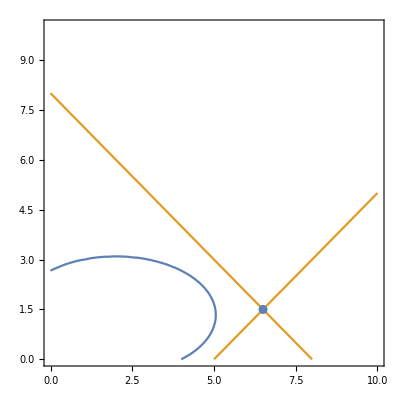

1)Дано:
	Цільова функція: f = -4 x1+x1^2-8 x2+3 x2^2 -> min
	Обмеження        g:(-10+2 x1-2 x2
-32+4 x1+4 x2) = 0
2)Знаходимо L = -4 x1+x1^2-8 x2+3 x2^2+(-10+2 x1-2 x2) λ1+(-32+4 x1+4 x2) λ2
3)Знаходимо всі часткові похідні від L і будуємо систему рівянь:
(-4+2 x1+2 λ1+4 λ2
-8+6 x2-2 λ1+4 λ2
-10+2 x1-2 x2
-32+4 x1+4 x2) = 0
4)Знаходимо її рішення:
(x1→13/2 | x2→3/2 | λ1→-2 | λ2→-5/4)
5)Знаходимо Гессіан для L:
(2 | 0
0 | 6)
6)Для кожного знайдено розв'язку перевіряємо його на екстремум:

Для Х =  {x1→13/2,x2→3/2,λ1→-2,λ2→-5/4}
Значення цільової функції в точці Х: f(X) = 11
Підставляємо Х в Гессіан:
(2 | 0
0 | 6)
Знаходимо кутові мінори Гессіана(від 1х1 до NxN):
{2,12}
Застосовуємо критерій Сільвестра. Згідно критерію Сільвестра матриця Гессе є додатньовизнчена. Х - точка локального мінімуму

7)Відповідь:

Х = {x1→13/2,x2→3/2,λ1→-2,λ2→-5/4} ,f(X) = 11

```mathematica
PositiveDefineList[list_]:=If[(FreeQ[list,_?Negative] && FreeQ[list,0]),True,False]
NegativeList[list_]:=If[(FreeQ[list,_?Positive] && FreeQ[list,0]),True,False]
NegativeDefineList[list_]:=If[(PositiveDefineList[list[[2;;-1;;2]]]&& NegativeList[list[[;;;;2]]]),True,False]
Lagrange[f0_,opt0_,g0_,numX0_,numG0_]:=Module[{f=f0,opt=opt0,g=g0,numX=numX0,numG=numG0},
λ:=Table[Symbol["λ"<>ToString[i]],{i,numG}];
x:=Table[Symbol["x"<>ToString[i]],{i,numX}];
var:=Join[x,λ];
extrMin:="додатньовизнчена. Х - точка локального мінімуму";
extrMax:="від'ємновизнчена. Х - точка локального максимуму";
extrNo:="невизначена";
L:=Total[g*λ]+f;
(*Знаходимо похідні від Л - будуємо систему рівнянь*)
S:=D[L,{var}];
(*Знаходимо рішення системи*)
X:=Solve[S==0,var];
Print[Solve[g==0,{x1,x2}],x/.X,x];
Print[Show[ContourPlot[{f==0,g==0},{x1,0,10},{x2,0,10}],ListPlot[x/.X,PlotMarkers->Automatic]]];
H:=D[L,{x,2}];
fX:=f/.X;
Print["1)Дано:",
"\n\tЦільова функція: f = ",f," -> ",opt,
"\n\tОбмеження        g:",g//MatrixForm," = 0",
"\n2)Знаходимо L = ",L,
"\n3)Знаходимо всі часткові похідні від L і будуємо систему рівянь:\n",S//MatrixForm," = 0",
"\n4)Знаходимо її рішення:\n",X//MatrixForm,
"\n5)Знаходимо Гессіан для L:\n",H//MatrixForm,
"\n6)Для кожного знайдено розв'язку перевіряємо його на екстремум:"
];
Xextr:=List[];
For[i=1,i≤Length[X],i++,
HX:=H/.X[[i]];
Silvester:=Table[Det[HX[[1;;j,1;;j]]],{j,numX}];
extremum:=If[PositiveDefineList[Silvester],extrMin,
If[NegativeDefineList[Silvester],extrMax,extrNo]];
AppendTo[Xextr,extremum];
Print["\n\nДля Х =  ",X[[i]],
"\nЗначення цільової функції в точці Х: f(X) = ",fX[[i]],
"\nПідставляємо Х в Гессіан:\n",HX//MatrixForm,
"\nЗнаходимо кутові мінори Гессіана(від 1х1 до NxN):\n",Silvester,
"\nЗастосовуємо критерій Сільвестра. Згідно критерію Сільвестра матриця Гессе є ", extremum];
];
If[opt=="max",
pos:=Position[fX,Max[fX]][[1]][[1]];
If[Xextr[[pos]]==extrMax,,pos:=extrNo];
,If[opt=="min",
pos:=Position[fX,Min[fX]][[1]][[1]];
If[Xextr[[pos]]==extrMin,,pos:=extrNo];
,opt:=opt]];
Print["\n7)Відповідь:"];
If[pos==extrNo,Print["Задача не має розв'язків"],Print["Х = ",X[[pos]]," ,f(X) = ",fX[[pos]]]];
]
f:= -4x1-8x2+x1^2+3x2^2
opt := "min"
g:={2x1-2x2-10,
       4x1+4x2-32}
numX:=2
numG:=2
Lagrange[f,opt,g,numX,numG]
```